Notebook for visually representing the parameterization of the stationary anisotropic diffusion matrix.

```mathematica
f[x_,y_]:={Cos[Mod[ArcTan[x,y],2π]/2],Sin[Mod[ArcTan[x,y],2π]/2]}(*Half angle field*)
```

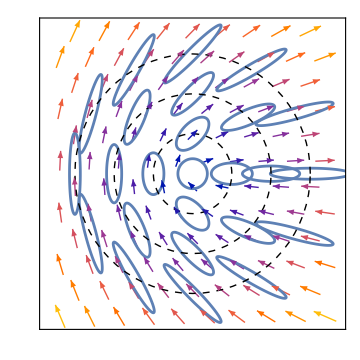

```mathematica
ell[x_,y_]:=Module[{a,b},
a=Exp[√(x^2+y^2)]/8f[x,y];
b=Exp[-2 √(x^2+y^2)]{-a[[2]],a[[1]]};
ParametricPlot[{x,y}+a Cos[t]+b Sin[t] ,{t,0,2 Pi},AxesLabel->{"x","y"},PlotRange->{-2,2}]
](*Ellipses with axes given by eigenspace and scaled to fit in image*)
rotations={π/2,π/4,π/6};(*determines eigenvectors of diffusion matrix*)
radiuses={1/3,2/3,1};(*determines eigenvalues of diffusion matrix*)
points=Flatten[Table[Table[radiuses[[i]]*{Cos[θ],Sin[θ]},{θ,0,2π-0.001,rotations[[i]]}],{i,1,Length[rotations]}],1];
ellipses=Flatten[{ell@@@points,ell[0.0001,0]}];
circles=Table[Graphics[{Dashed,Circle[{0,0},radiuses[[i]]]}],{i,1,Length[radiuses]}];
r=1.25;
vp=VectorPlot[Exp[√(x^2+y^2)]f[x,y],{x,-r,r},{y,-r,r},Axes->False,VectorScaling->Automatic,VectorPoints->10,VectorSizes->1,ImageSize->Medium,FrameTicks->None,Frame->True,VectorColorFunction->Automatic,VectorStyle->Orange];
a=Show[{vp,ellipses,circles},ImageSize->Medium]
```